```mathematica
(* 1.naloga *)
(*Izračunajte vrednost določenega integrala Vnesite vrednost integrala na decimalk natančno. *)
Clear["Global`*"]
NIntegrate[(x^2+4)/(x^2+1),{x,0,1}]
```

3.35619

{{x→1/8 (37-√105)},{x→1/8 (37+√105)}}

{1/8 (37-√105),1/8 (37+√105)}

{{x→3},{x→7}}

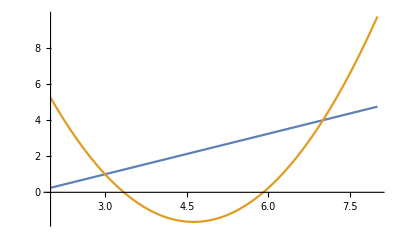

10.66667

```mathematica
(* 2.naloga *)
(* Izračunajte ploščino območja med premico in parabolo. *)
Clear["Global`*"]
pr1 = 3x/4-5/4;
par1=x^2-37x/4+79/4;
nic=Solve[par1==0, x]
nicle= nic[[All, 1,2]]
pres1 = Solve[pr1==par1,x]

Plot[{pr1,par1}, {x,2,8}]
N[Integrate[pr1, {x,3,7}]+Abs[Integrate[par1, {x, nicle[[1]],nicle[[2]]}]]- Integrate[par1, {x,3,nicle[[1]]}]-Integrate[par1, {x,nicle[[2]],7}],7]
```

(-2-3 x)/((-3+x) (2+x))

-3.37422

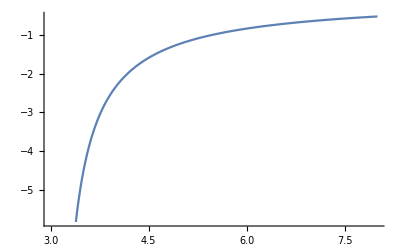

```mathematica
(* 3.naloga *)
(*Izračunajte vrednost določenega integrala Vnesite vrednost integrala na decimalk natančno. *)
Clear["Global`*"]
en1=(-3x-2)/((x-3)(x+2))
NIntegrate[(-3x-2)/((x-3)(x+2)),{x,4,7}]

Plot[en1, {x, 3,8}]
```

```mathematica
(* 4.naloga *)
(*Razvijte funkcijo pod integralom v Taylorjevo vrsto do vključno potence x^3 in izračunajte približno vrednost integrala*)
Clear["Global`*"]
fint = (1-E^(-x/4))/x
(* numerična rešitev *)
NIntegrate[fint, {x,0,1/2}]
(* Taylorjeva vrsta *)
N[Integrate[Normal[Series[fint,{x,0,3}]],{x,0,1/2}],6]
```

(1-ⅇ^(-x/4))/x

0.1212

0.1212

```mathematica
(* 5.naloga *)
(* Določite vrednost funkcije v stacionarni točki.Rezultat vnesite na decimalk natančno. *)
Clear["Global`*"]
f[x_,y_]=E^(3x)(4x+y^2+6y)
fx=D[f[x,y],x]
fy=D[f[x,y],y]
sol=Solve[{fx==0,fy==0},{x,y}]
stt= N[E^(3x)(4x+y^2+6y)/.sol ,9]
```

ⅇ^(3 x) (4 x+6 y+y^2)

4 ⅇ^(3 x)+3 ⅇ^(3 x) (4 x+6 y+y^2)

ⅇ^(3 x) (6+2 y)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→23/12,y→-3}}

{-418.92088}

```mathematica
(* 6.naloga *)
(* Izračunajte dolžino loka krivulje. Vnesite vrednost za dolžino loka na decimalk natančno. *)
Clear["Global`*"]
y=2/3x^(3/2)

FullSimplify[Integrate[Sqrt[1+D[y,x]^2], {x, 0, 3}]] //N
```

(2 x^(3/2))/3

4.66667

1883/1140

1883/1140-(40 x)/57

1883/800

1.02303

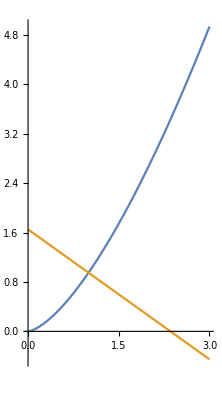

```mathematica
(* 7.naloga *)
(* Izračunajte ploščino lika,omejenega s krivuljo, normalo na to krivuljo v točki in abscisno osjo.Vnesite vrednost za ploščino na decimalk natančno. *)
Clear["Global`*"]
y=19/20x^(3/2);
xn=1;
yn = y/.x->xn; (*damo v y x=1 da veš kok je vrednost v tej točki*)
kt=D[y,x]/.x->xn; (*odvod od funkcije y v 1 za smerni koef tangente.*)(* odvod je smerni koeficient tangente *)
kn = -1/kt; (* smerni koeficient normale*)
nn = yn-(kn*xn) (*seka y os*)
ynormale = kn*x+nn
b=x/.Flatten[Solve[ynormale==0,x]]
S=N[Integrate[y,{x,0,1}]+ Integrate[ynormale,{x,1,b}],6]
Plot[{y,ynormale},{x,0,3},AspectRatio->Automatic]
```

```mathematica
(* 8.naloga *)
(* Izračunajte konvergenčni polmer potenčne vrste *)
Clear["Global`*"]
(* Splošni člen *)
a[n_]:=4^n/Sqrt[4n-1]
R=Limit[Abs[a[n]/a[n+1]],n->Infinity] //N
```

0.25

```mathematica
(* 9.naloga *)
(* Izračunajte prostornino telesa,ki ga dobimo,če zavrtimo krivuljo na intervalu okrog osi. *)
Clear["Global`*"]
y=Sqrt[(5x+2)*Sin[x]/Pi]
V=N[Pi*Integrate[y^2, {x,0,Pi}],7]
Plot[f, {x,0,4}]
```

(√((2+5 x) Sin[x]))/(√π)

19.70796

-Graphics-

```mathematica
(* 10.naloga *)
(* Izračunajte vrednost tretjega parcialnega fxyy odvoda funkcije v točki T(-3,-1)*)
Clear["Global`*"]
f[x_,y_]=x^4+2y x^3-4x^2y^2-4x y^3+y^4
fxyy=Simplify[D[f[x,y], x,y,y]]
res=fxyy /.x->-3/.y->-1
```

x^4+2 x^3 y-4 x^2 y^2-4 x y^3+y^4

-8 (2 x+3 y)

72